# Tworzenie i optymalizacja filtrów IIR

## Raport 2 (12.11.2016)

Uniwersytet Jagielloński – Zakład Fotoniki

## Wstęp

### Metoda tworzenia filtrów IIR

Najpopularniejszą metodą tworzenia filtrów cyfrowych ze sprzężeniem zwrotnym (Infinite Impule Response – IIR) jest metoda polegająca na stworzeniu wpierw ich analogowych prototypów, a następnie przejściu (za pomocą transformaty biliniowej) do ich cyfrowych odpowiedników.
Wśród powszechnie znanych typów filtrów analogowych znajdują się:

filtry Butterworth’a

filtry Czebyszewa I/II

filtry Eliptyczne

### Badanie stabilności filtrów - porównanie filtrów analogowych i cyfrowych

Układ analogowy jet stabilny, jeżeli bieguny jego transmitancji leżą w lewej półpłaszczyźnie płaszczyzny zespolonej.

Układ dyskretny jest stabilny, jeżeli bieguny jego transmitancji leżą wewnątrz okręgu jednostkowego na płaszczyźnie zespolonej.

Dla układu analogowego osią częstotliwości jest oś urojona s=jω.
Dla układu dyskretnego częstotliwość zmiania się po okręgu jednostkowym z=e^jΩ.

W przypadku biegunów na osi (dla analogowych) lub na okręgu (dla dyskretnych) stabilność jest warunkowa, a układ odpowiada oscylacją.

# Część I

## Projektowanie filtrów analogowych Butterwortha i Czebyszewa

Podczas projektowania korzystamy z oznaczeń przedstawionych na rysunku poniżej

Częstotliwość końca pasma przepustowego (f_P) w dB

Największe dopuszczalne tłumienie w paśmie przepustowym (A_p) dla filtru Czebyszewa ten parametr określa jednocześnie dopuszczalne zafalowanie charakterystyki amplitudowej w paśmie przepustowym (w kHz)

Częstotliwość początku pasma zaporowego (f_R) w dB

Wymagane minimalne tłumienie w paśmie zaporowym (A_R) (w kHz)

```mathematica
Ap=0.5; 
fp=3;
Ar=20;
fr=7;
```

### Obliczenie rzędu filtra

#### Współczynnik selektywności k

k=f_P/f_R

```mathematica
k[fp_,fr_]:=fp/fr;
```

#### Współczynnik dyskryminacji d

d=√((10^(0.1 A_P)-1)/(10^(0.1 A_R)-1))

```mathematica
d[Ap_,Ar_]:=√((10^(0.1 Ap)-1)/(10^(0.1 Ar)-1));
```

Rząd filtra Butterwortha oblicza się ze współczynników k i d

n=(|log d|)/(|log k|)

```mathematica
nbutt[d_,k_]:=Abs[Log[d]]/Abs[Log[k]];
```

```mathematica
nb=nbutt[d[Ap,Ar],k[fp,fr]]
```

3.95298

Rząd filtra Czebyszewa określa się z podobnego wzoru:

n=(arc cosh(1/d))/(arc cosh(1/k))

```mathematica
nczeb[d_,k_]:=ArcCos[1/d]/ArcCos[1/k];
```

```mathematica
nc=nczeb[d[Ap,Ar],k[fp,fr]]
```

2.71107+0. ⅈ

Rząd filtru nie może być ułamkowy, więc zaokrąglamy w górę.

```mathematica
nb=Ceiling[nb]
nc=Ceiling[nc]
```

4

3

Rząd filtr Czebyszewa będzie zawsze mniejszy lub równy rzędowi filtru Butterwortha.

### Częstotliwość graniczna

W dolnoprzepustowym filtrze Czebyszewa jest to częstotliwość, dla której tłumienie filtru nie przekracza założonych zafalowań charakterystyki. A więc poprostu f_P

f_g=f_P

```mathematica
fgc=fp;
```

Dla filtru Butterwortha, częstotliwość graniczna to taka dla której następuje spadek wzmocnienia o 3 dB względem sygnału stałego (o częstotliowści 0). Jest ona większa od f_P jeżeli A_P jest mniejsze niż 3 dB. Można ją określić ze wzoru

f_g=f_P/((10^(0.1 A_P)-1)^(1/(2n)))

```mathematica
fg[fp_,Ap_,n_]:=fp/(10^(0.1 Ap)-1)^(1/(2n));
```

```mathematica
fgb=fg[fp,Ap,4]
```

3.90228

### Filtr prototypowy

Filtr prototypowy ≡ filtr anaologowy którego częstotliwość graniczna wynosi 1 Hz.

#### Butterworth

Kradrat charakterystyki amplitudowej definiuje się następująco

(|H(jω)|)^2=1/(1+(jω/j ω_(3 dB))^(2N))

|H(jω)|=√(1/(1+(jω/j ω_(3 dB))^(2N)))

gdzie ω_(3 dB) jest pulsacją, dla której charakterystyka amplitudowa opada do poziomu 1/(√2) (3 dB w skali decybelowej 20 log_10(1/√2)=-3dB. Rozważając zera mianownika:

1+(s/j ω_(3dB))^(2N)=0

Otrzymujemy bieguny transmitancji filtra Butterwortha:

```mathematica
sol=Solve[1+(s/(ⅈ ω))^(2NN)==0&&NN>0,s,Complexes]
```

{{s→ConditionalExpression[ⅈ ⅇ^((ⅈ (π+2 π C[1]))/(2 NN)) ω,(C[1]∈Integers&&-1+2 NN-2 C[1]≥0&&C[1]≥0)||(C[1]∈Integers&&C[1]≤-1&&1+2 NN+2 C[1]>0)]}}

```mathematica
sol[[1,1,2,1]]
```

ⅈ ⅇ^((ⅈ (π+2 π C[1]))/(2 NN)) ω

ω_(3dB)ⅇ^(j (π/(2N))(2k+N-1))

Do filtra wybieramy tylko te znajdujące się w lewej półpłaszczyźnie

```mathematica
roots[k_,N_]:=Exp[ⅈ(π/(2N))(2k+N-1)];
NN=2;
rootsbutt=N@Table[roots[i,NN],{i,0,NN}];
selrootbutt=s-Select[rootsbutt,Re[#]<=0&];
1/Times[selrootbutt/.{List->Sequence}]
```

1/(((0.707107-0.707107 ⅈ)+s) ((0.707107+0.707107 ⅈ)+s))

Z równania (Section.EquationNumbered) otrzymujemy:

20 log_10(1/√(1+(ω_p/ω_(3dB))^(2N)))=-A_P

20 log_10(1/√(1+(ω_s/ω_(3dB))^(2N)))=-A_R

Skąd rząd filtru:

N=1/2 log_10((10^(A_P/10)-1)/(10^(A_R/10)-1))/log_10(ω_p/ω_s)

ω_(3dB)=ω_pass/((10^(A_P/10)-1)^(1/(2N)))

### Całość dla filtru Butterworth

```mathematica
Ap=0.5; 
fp=3;
As=20;
fs=7;
```

```mathematica
NButterworth[Ap_,As_,fp_,fs_]:=Ceiling[1/2 Log10[(10^(Ap/10)-1)/(10^(As/10)-1)]/Log10[fp/fs]];
```

```mathematica
f3dB[fp_,Ap_,NN_]:=fp/((10^(Ap/10)-1)^(1/(2NN)));(**pulsacja**)
```

```mathematica
NN=NButterworth[Ap,As,fp,fs]
f3dB[fp,Ap,NN]
```

4

3.90228

```mathematica
roots[k_,N_]:=f3dB[fp,Ap,NN]Exp[ⅈ(π/(2N))(2k+N-1)];
rootsbutt=N@Table[roots[i,NN],{i,0,NN}];
selrootbutt=s-Select[rootsbutt,Re[#]<=0&];
ButterworthFilter[ω_]:=f3dB[fp,Ap,NN]^NN/Times[selrootbutt/.{List->Sequence}]/.{s->ⅈω}
```

231.885/(((1.49334-3.60523 ⅈ)+ⅈ ω) ((1.49334+3.60523 ⅈ)+ⅈ ω) ((3.60523-1.49334 ⅈ)+ⅈ ω) ((3.60523+1.49334 ⅈ)+ⅈ ω))

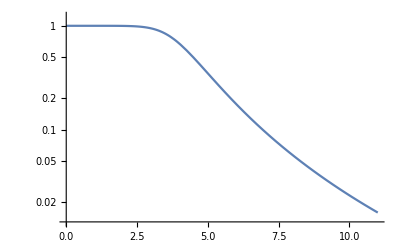

```mathematica
ButterworthFilter[ω]
LogPlot[Abs[ButterworthFilter[ω]],{ω,0,11},PlotRange->Full]
```

### Filtr Czebyszewa

(|H(jω)|)^2=1/(1+ϵ^2 V_N^2(ⅈω/ⅈ ω_(3dB)))

Gdzie

V_N(x)=Piecewise[{{cos(N arccos(x)), |x|≤1}, {cosh(Narccosh(x)), |x|>1}}]

Jest to filtr I typu. Charakterystyka jest równomiernie falista w paśmie przepustowym.
Amplituda zafalowania jest regulowana parametrem ϵ. 
W paśmie zaporowym charakterystyka opada monotonicznie

Dla filtru typu II jest odwrotnie. Charakterystyka jest płaska w paśmie przepustowym i równomiernie falista w paśmie zaporowym. 
Parametr ϵ reguluje amplitudę zafalowania charakterystyki amplitudowej w paśmie zaporowym.

(|H(jω)|)^2=1/(1+1/(ϵ^2 V_N^2(ⅈω_(3dB)/ⅈω)))

### Filtr eliptyczny

Do aproksymacji idealnej, prostokątnej charakterystyki częstotliwościowej w przypadku filtra eliptycznego stosuje się eliptyczną funkcję Jacobiego. 
Charakterystyka amplitudowa filtra eliptycznego jest równomiernie falista w paśmie przepustowym i zaporowym. Filtr eliptyczny opisują 4 parametry: N – rząd filtra, ω - krawędź pasma przepustowego, A_P oraz A_R.

### Transformacja częstotliwości

Po zaprojektowaniu analogowego filtru dolnoprzepustowego możemy utworzyć inne filtry korzystając z następującej tabeli:

Low pass | s'=s/ω_0
High pass | s'=ω_0/s
Band pass | s'=ω_0/Δω((s/ω_0)^2+1)/(s/ω_0)
Band stop | s'=Δω/ω_0(s/ω_0)/((s/ω_0)^2+1)

where Δω=ω_2-ω_1 and ω_0=√(ω_1 ω_2)

## Przykładowy projekt filtru dolnoprzepustowego

Zakładamy wartości parametrów filtru:

częstotliwość próbkowania f_pr=100Hz

krawędź pasma przepustowego f_1=20Hz

krawędź pasma zaporowego f_2=25Hz

nieliniowość charakterystyki w paśmie przepustowym A_p=3 dB

nieliniowość charakterystyki w paśmie zaporowym A_s=30dB

Przeliczenie częstotliwości filtra cyfrowego f_1 i f_2 na pulsację Ω w radianach:

Ω_1=2π f_1/f_pr=2π 20/100=1.2566 rad

Ω_2=2π f_2/f_pr=2π 25/100=1.5708 rad

```mathematica
A1=3;
f1=20;
A2=30;
f2=25;
fp=100;
```

```mathematica
Ω1=N@2π f1/fp
Ω2=N@2π f2/fp
```

1.25664

1.5708

### Krawędź pasma filtru analogowego

ω_1=2/(2Δt)tan(Ω_1/2)=2/(1/100)tan(1.2566/2)=145.3085 rad/s

ω_2=200 rad/s

```mathematica
ω1=2/(1/fp)Tan[Ω1/2]
ω2=2/(1/fp)Tan[Ω2/2]
fa1=1/(2π)ω1;
fa2=1/(2π)ω2;
```

145.309

200.

### Określenie parametrów filtru analogowego na podstawie podanych wymagań

```mathematica
NButterworth[Ap_,As_,fp_,fs_]:=Ceiling[1/2 Log10[(10^(Ap/10)-1)/(10^(As/10)-1)]/Log10[fp/fs]];
```

```mathematica
f3dB[fp_,Ap_,NN_]:=fp/((10^(Ap/10)-1)^(1/(2NN)));(**pulsacja**)
```

```mathematica
NN=NButterworth[A1,A2,fa1,fa2]
N@f3dB[ω1,A1,NN]
```

11

145.34

```mathematica
roots[k_,N_]:=f3dB[ω1,A1,NN]Exp[ⅈ(π/(2N))(2k+N-1)];
rootsbutt=N@Table[roots[i,NN],{i,0,NN}];
selrootbutt=s-Select[rootsbutt,Re[#]<=0&];
ButterworthFilter[ω_]:=f3dB[ω1,A1,NN]^NN/Times[selrootbutt/.{List->Sequence}]
```

### Filtr analogowy

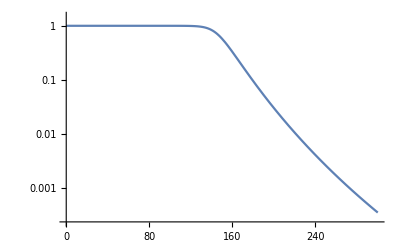

```mathematica
LogPlot[{Abs[ButterworthFilter[s]/.{s->ⅈ ω}]},{ω,0,300},PlotRange->Full]
```

### Przejście na filtr cyfrowy (w dziedzienie pulsacji/częstości)

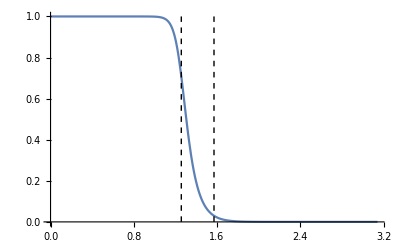

```mathematica
Plot[Abs[ButterworthFilter[s]/.{s->2fp(1-z^-1)/(1+z^-1)}/.{z->ⅇ^ⅈΩ}],{Ω,0,π},PlotRange->Full,Epilog->{Dashing[0.01],Line[{{Ω1,0},{Ω1,1}}],Line[{{Ω2,0},{Ω2,1}}]}]
```

### Filtr cyfrowy w dziedzinie częstotliwości

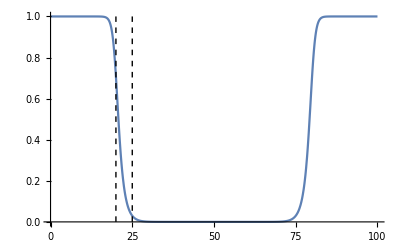

```mathematica
Plot[Abs[ButterworthFilter[s]/.{s->2fp(1-z^-1)/(1+z^-1)}/.{z->ⅇ^ⅈΩ}/.{Ω->f (2π)/fp}],{f,0,100},PlotRange->Full,Epilog->{Dashing[0.01],Line[{{f1,0},{f1,1}}],Line[{{f2,0},{f2,1}}]}]
```

## Badanie reakcji filtru Butterworth na zmianę częstotliwości odcięcia

```mathematica
Manipulate[NButterworth[A1,A2,x,y],{x,0,100},{y,x,100},{A1,0,100,1},{A2,0,100,1}]
```

Obserwacja: im częstotliwości bliższe sobie, a za tem im bardziej stromy filtr tym wyższy rząd filtru Butterworth’a jest wymagany.

Oprócz tego dla:
(2.2,2.3)→N=78
(22.2,22.3)→N=769
(82.2, 82.3)→N=2843
a więc rząd filtru rośnie także z częstotliwością przy stałej różnicy f_2-f_1.

# Cześć II

## Badanie błędów dyskretyzacji filtrów cyfrowych

### Definicje

```mathematica
Δω=0.3;
ωmin=0.1;
ωmax=1.5;
bity=6;
```

#### Funkcje dyskretyzujące

```mathematica
DiscretizeList[x_,max_,bits_]:=If[ #≥0 ,1,-1]Round[(Abs[#]/max)(Power[2,bits-1]-1)] max/(Power[2,bits-1]-1) &/@x;
DiscretizeComplexList[x_,y_,bits_]:=Module[{xD,yD,coeffD,max},
If[y=={},{},
max=Max[Abs[Join[Re@x,Im@x,Re@y,Im@y]]];
xD=DiscretizeList[Re@x,max,bits]+ⅈ DiscretizeList[Im@x,max,bits];
yD=DiscretizeList[Re@y,max,bits]+ⅈ DiscretizeList[Im@y,max,bits];
{xD,yD}]
];
DiscretizeModelCoeffs[tf_,bits_]:=Module[{zeros,poles,zerosD,polesD},
	zeros=CoefficientList[Numerator[TransferFunctionExpand[tf][z]][[1,1]],z];
poles=CoefficientList[Denominator[TransferFunctionExpand[tf][z]][[1,1]],z];
{zerosD,polesD}=DiscretizeComplexList[zeros,poles,bits];
	Chop[FromDigits[Reverse[zerosD],z]/(FromDigits[Reverse[polesD],z])]
];
```

#### Funkcja błędu

```mathematica
CalcError[filtr_,filtrD_]:=Sqrt[NIntegrate[Abs[filtr-filtrD]^2,{Ω,0,π},AccuracyGoal->5,MaxRecursion->20]/NIntegrate[Abs[filtr]^2,{Ω,0,π},AccuracyGoal->5,MaxRecursion->20]];
```

Szybsza wersja:

```mathematica
CalcError[filtr_,filtrD_]:=Sqrt[Total[Abs[Table[filtr,{Ω,0,π,0.001}]-Table[filtrD,{Ω,0,π,0.001}]]^2]/Total[Abs[Table[filtr,{Ω,0,π,0.001}]]^2]];
```

### Ustalenie postaci filtrów cyfrowych

Poniżej znajdują się definicje filtrów analogowych i ich cyfrowych odpowiedników w postaci tabel dla rzędu N={1,2,...7} oraz częstości ω={ωmin, ωmax, Δω}

#### Butterworth

```mathematica
bmodels=Table[{n,ω,TransferFunctionFactor@ButterworthFilterModel[{"Lowpass" ,n,ω},s]},{n,1,7,1},{ω,ωmin,ωmax,Δω}];
DGbmodels=Table[{n,ω,TransferFunctionFactor@ToDiscreteTimeModel[ButterworthFilterModel[{"Lowpass" ,n,ω},s],1]},{n,1,7,1},{ω,ωmin,ωmax,Δω}];
```

#### Chebyshev 1

```mathematica
c1models=Table[{n,ω,TransferFunctionFactor@Chebyshev1FilterModel[{"Lowpass" ,n,ω},s]},{n,1,7,1},{ω,ωmin,ωmax,Δω}];
DGc1models=Table[{n,ω,TransferFunctionFactor@ToDiscreteTimeModel[Chebyshev1FilterModel[{"Lowpass" ,n,ω},s],1]},{n,1,7,1},{ω,ωmin,ωmax,Δω}];
```

#### Chebyshev 2

```mathematica
c2models=Table[{n,ω,TransferFunctionFactor@Chebyshev2FilterModel[{n,ω},s]},{n,1,7,1},{ω,ωmin,ωmax,Δω}];
DGc2models=Table[{n,ω,TransferFunctionFactor@ToDiscreteTimeModel[Chebyshev2FilterModel[{n,ω},s],1]},{n,1,7,1},{ω,ωmin,ωmax,Δω}];
```

#### Eliptic

```mathematica
emodels=Table[{n,ω,TransferFunctionFactor@EllipticFilterModel[{n,ω},s]},{n,1,7,1},{ω,ωmin,ωmax,Δω}];
DGemodels=Table[{n,ω,TransferFunctionFactor@ToDiscreteTimeModel[EllipticFilterModel[{n,ω},s],1]},{n,1,7,1},{ω,ωmin,ωmax,Δω}];
```

### Dyskretyzacja

```mathematica
DGbmodelsDc2=Map[{#[[1]],#[[2]],DiscretizeModelCoeffs[#[[3]],bity]}&,DGbmodels,{2}];
```

```mathematica
DGc1modelsDc2=Map[{#[[1]],#[[2]],DiscretizeModelCoeffs[#[[3]],bity]}&,DGc1models,{2}];
```

```mathematica
DGc2modelsDc2=Map[{#[[1]],#[[2]],DiscretizeModelCoeffs[#[[3]],bity]}&,DGc2models,{2}];
```

```mathematica
DGemodelsDc2=Map[{#[[1]],#[[2]],DiscretizeModelCoeffs[#[[3]],bity]}&,DGemodels,{2}];
```

### Wyniki

```mathematica
NicePlot[modelA_,modelB_,Nind_,ωind_]:=Plot[{Abs[modelA[[Nind,ωind]][[3]][ⅇ^(ⅈ ω)]]^2,Abs[(modelB[[Nind,ωind]][[3]])]^2/.{z->ⅇ^(ⅈ ω)}},{ω,0,π},AxesLabel->{ω,None},GridLines->Automatic,AspectRatio->1/3,PlotRange->Full, PlotLegends->{"Przed dyskretyzacją","Po dyskretyzacji"},PlotLabel->"Przykładowy efekt dyskretyzacji dla N="<>ToString[modelA[[Nind,ωind]][[1]]]<>", ω="<>ToString[modelA[[Nind,ωind]][[2]]]<>" i "<> ToString[bity]<>" bitów" ]
```

#### Butterworth

Funkcje błędu w zależności od rzędu filtra i częstości granicznej:

```mathematica
errors=Flatten[MapThread[{#1[[1]],#1[[2]],First@Flatten@CalcError[Abs@#1[[3]][ⅇ^(ⅈ Ω)],Abs@#2[[3]]/.{z->I Ω}]}&,{DGbmodels,DGbmodelsDc2},2],1];
```

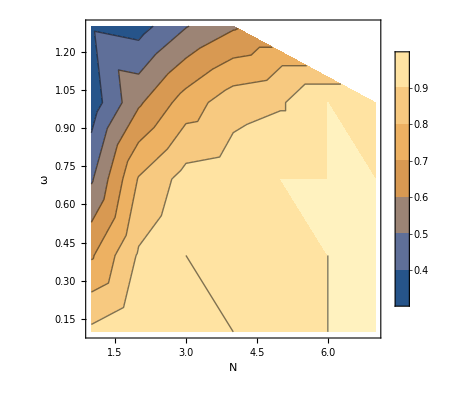

```mathematica
ListContourPlot[errors,FrameLabel->{"N","ω","Error"},PlotRange->Full,PlotLegends->Automatic,LabelStyle->Directive[Bold]]
```

Poniżej dwa przykłady:

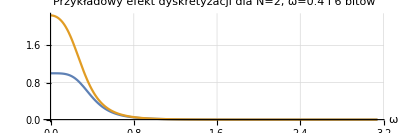

```mathematica
NicePlot[DGbmodels,DGbmodelsDc2,2,2]
```

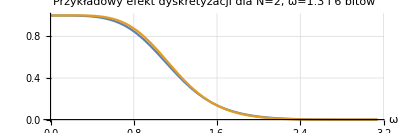

```mathematica
NicePlot[DGbmodels,DGbmodelsDc2,2,5]
```

#### Chebyshev 1

Funkcje błędu w zależności od rzędu filtra i częstości granicznej:

```mathematica
errors=Flatten[MapThread[{#1[[1]],#1[[2]],First@Flatten@CalcError[Abs[#1[[3]][ⅇ^(ⅈ Ω)]],Abs[#2[[3]]]/.{z->I Ω}]}&,{DGc1models,DGc1modelsDc2},2],1];
```

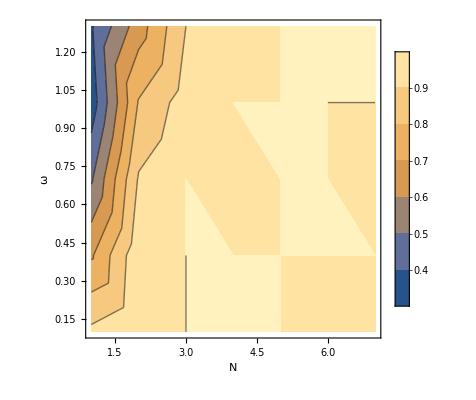

```mathematica
ListContourPlot[errors,FrameLabel->{"N","ω","Error"},PlotRange->Full,PlotLegends->Automatic,LabelStyle->Directive[Bold]]
```

Poniżej dwa przykłady:

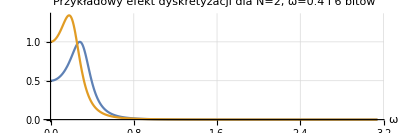

```mathematica
NicePlot[DGc1models,DGc1modelsDc2,2,2]
```

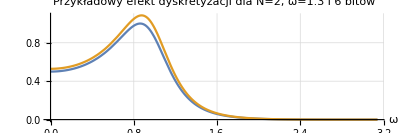

```mathematica
NicePlot[DGc1models,DGc1modelsDc2,2,5]
```

#### Chebyshev 2

Funkcje błędu w zależności od rzędu filtra i częstości granicznej:

```mathematica
errors=Flatten[MapThread[{#1[[1]],#1[[2]],First@Flatten@CalcError[Abs@#1[[3]][ⅇ^(ⅈ Ω)],Abs@#2[[3]]/.{z->I Ω}]}&,{DGc2models,DGc2modelsDc2},2],1];
```

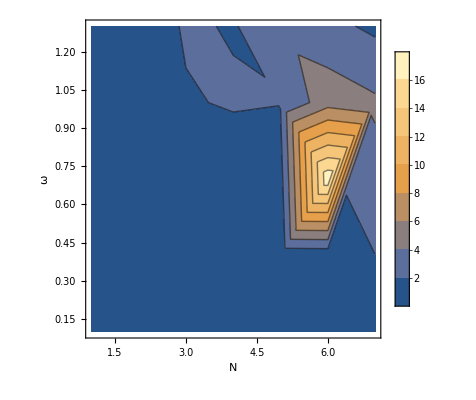

```mathematica
ListContourPlot[errors,FrameLabel->{"N","ω","Error"},PlotRange->Full,PlotLegends->Automatic,LabelStyle->Directive[Bold]]
```

Powiększam fragment w okolicy małych częstości gdzie błędy są mniejsze od 1.

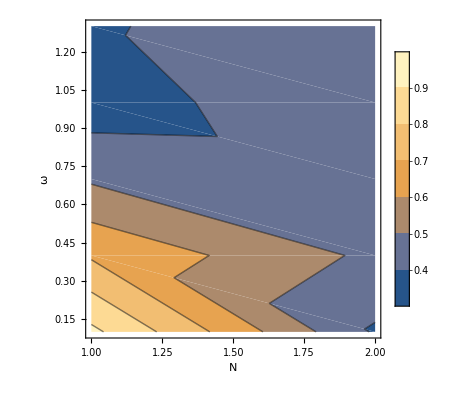

```mathematica
ListContourPlot[errors[[1;;10]],FrameLabel->{"N","ω","Error"},PlotRange->Full,PlotLegends->Automatic,LabelStyle->Directive[Bold]]
```

Poniżej dwa przykłady:

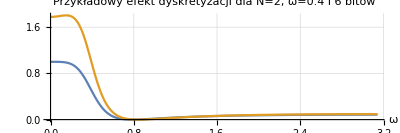

```mathematica
NicePlot[DGc2models,DGc2modelsDc2,2,2]
```

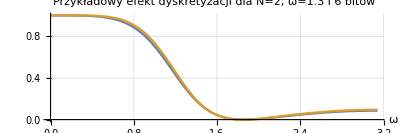

```mathematica
NicePlot[DGc2models,DGc2modelsDc2,2,5]
```

#### Eliptic

Funkcje błędu w zależności od rzędu filtra i częstości granicznej:

```mathematica
errors=Flatten[MapThread[{#1[[1]],#1[[2]],First@Flatten@CalcError[Abs@#1[[3]][ⅇ^(ⅈ Ω)],Abs@#2[[3]]/.{z->I Ω}]}&,{DGemodels,DGemodelsDc2},2],1];
```

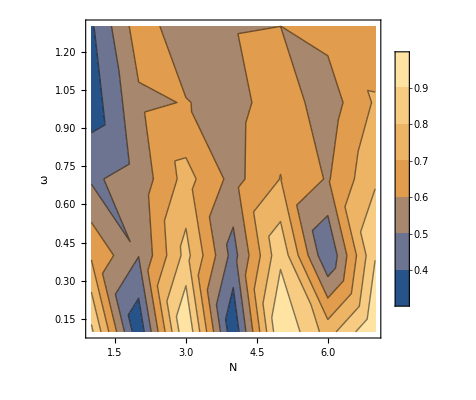

```mathematica
ListContourPlot[errors,FrameLabel->{"N","ω","Error"},PlotRange->Full,PlotLegends->Automatic,LabelStyle->Directive[Bold]]
```

Poniżej dwa przykłady:

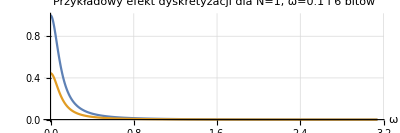

```mathematica
NicePlot[DGemodels,DGemodelsDc2,1,1]
```

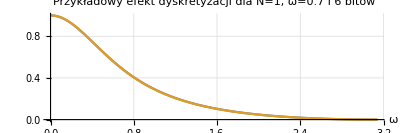

```mathematica
NicePlot[DGemodels,DGemodelsDc2,1,3]
```

## Badanie stabilności dyskretyzowanych filtrów cyfrowych

### Ustalenie postaci filtrów cyfrowych

Poniżej znajdują się definicje filtrów analogowych i ich cyfrowych odpowiedników w postaci tabel dla rzędu N={1,2,...7} oraz częstości ω={ωmin, ωmax, Δω}

#### Definicje

```mathematica
Δω=0.3;
ωmin=0.1;
ωmax=2.0;
```

#### Butterworth

```mathematica
bmodels=Table[TransferFunctionFactor@ButterworthFilterModel[{"Lowpass" ,n,ω},s],{n,1,7,1},{ω,ωmin,ωmax,Δω}];
DGbmodels=Table[TransferFunctionFactor@ToDiscreteTimeModel[ButterworthFilterModel[{"Lowpass" ,n,ω},s],1],{n,1,7,1},{ω,ωmin,ωmax,Δω}];
```

#### Chebyshev 1

```mathematica
c1models=Table[TransferFunctionFactor@Chebyshev1FilterModel[{"Lowpass" ,n,ω},s],{n,1,7,1},{ω,ωmin,ωmax,Δω}];
DGc1models=Table[TransferFunctionFactor@ToDiscreteTimeModel[Chebyshev1FilterModel[{"Lowpass" ,n,ω},s],1],{n,1,7,1},{ω,ωmin,ωmax,Δω}];
```

#### Chebyshev 2

```mathematica
c2models=Table[TransferFunctionFactor@Chebyshev2FilterModel[{n,ω},s],{n,1,7,1},{ω,ωmin,ωmax,Δω}];
DGc2models=Table[TransferFunctionFactor@ToDiscreteTimeModel[Chebyshev2FilterModel[{n,ω},s],1],{n,1,7,1},{ω,ωmin,ωmax,Δω}];
```

#### Eliptic

```mathematica
emodels=Table[TransferFunctionFactor@EllipticFilterModel[{n,ω},s],{n,1,7,1},{ω,ωmin,ωmax,Δω}];
DGemodels=Table[TransferFunctionFactor@ToDiscreteTimeModel[EllipticFilterModel[{n,ω},s],1],{n,1,7,1},{ω,ωmin,ωmax,Δω}];
```

### Funkcje pomocnicze

Pomocnicza funkcja by pobrać bieguny zdyskretyzowanych filtrów

```mathematica
ExtractPoles[tf_]:=Module[{coeff},
coeff=First[Flatten[ExpandNumerator@Numerator[tf]]];
coeff=If[Length[coeff]>0,coeff[[1]],coeff];
(z/.Solve[Denominator@(tf/coeff)==0,z])
]
```

Ustalamy ilość bitów do symulacji

```mathematica
bity=6;
```

Przygotowywuję funkcję rysującą bieguny i zaznaczającą na czerwono te w których bieguny filtru zdyskretyzowanego wychodzą poza okrąg jednostkowy.

```mathematica
PlotPoles[poles_,poles2_]:=ListPlot[{Transpose[{Re[poles],Im[poles]}],Transpose[{Re[poles2],Im[poles2]}]},PlotRange->1.2{{-1,1},{-1,1}},PlotStyle->{PointSize[Large]},Background->If[Count[poles2,_?(Abs[#]≥1&),{1}]>0,LightRed,White],PlotMarkers->{Automatic,Medium},AxesOrigin->{0,0},Epilog->{Green,Circle[]},AspectRatio->Automatic]
```

```mathematica
AsymptoticallyStableQ[tfm_?ContinuousTimeModelQ]:=If[
Count[TransferFunctionPoles[tfm],Complex[x_?NonNegative,_]|x_?NonNegative,{3}]>0,False,True]
AsymptoticallyStableQ[tfm_?DiscreteTimeModelQ]:=If[
Count[TransferFunctionPoles[tfm],_?(Abs[#]≥1&),{3}]>0,False,True]
```

### Dyskretyzacja współczynników filtru cyfrowego

#### Definicje

```mathematica
DiscretizeList[x_,max_,bits_]:=If[ #≥0 ,1,-1]Round[(Abs[#]/max)(Power[2,bits-1]-1)] max/(Power[2,bits-1]-1) &/@x;
DiscretizeComplexList[x_,y_,bits_]:=Module[{xD,yD,coeffD,max},
If[y=={},{},
max=Max[Abs[Join[Re@x,Im@x,Re@y,Im@y]]];
xD=DiscretizeList[Re@x,max,bits]+ⅈ DiscretizeList[Im@x,max,bits];
yD=DiscretizeList[Re@y,max,bits]+ⅈ DiscretizeList[Im@y,max,bits];
{xD,yD}]
];
DiscretizeModelCoeffs[tf_,bits_]:=Module[{zeros,poles,zerosD,polesD},
	zeros=CoefficientList[Numerator[TransferFunctionExpand[tf][z]][[1,1]],z];
poles=CoefficientList[Denominator[TransferFunctionExpand[tf][z]][[1,1]],z];
{zerosD,polesD}=DiscretizeComplexList[zeros,poles,bits];
	Chop[FromDigits[Reverse[zerosD],z]/(FromDigits[Reverse[polesD],z])]
];
```

#### Testy

```mathematica
{a,c}=DiscretizeComplexList[{1,2,3},{ⅈ,ⅈ 2,ⅈ 3},2]
```

{{0,3,3},{0,3 ⅈ,3 ⅈ}}

Dyskretyzujemy na poziomie filtrów cyfrowych

```mathematica
buttModel=TransferFunctionExpand@DGbmodels[[2,2]]
```

(0.0302379+0.0604758 z+0.0302379 z^2)/((0.572371+0. ⅈ)-(1.45142+0. ⅈ) z+z^2)1TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#z110.0302379108436653840.57237136387059961FalseFalseFalseAutomaticNoneAutomatic

```mathematica
polesButt=TransferFunctionPoles[buttModel][[1,1]]
```

{0.72571-0.213814 ⅈ,0.72571+0.213814 ⅈ}

```mathematica
buttModelD=N@DiscretizeModelCoeffs[buttModel,bity]
```

(0.04682+0.04682 z+0.04682 z^2)/(0.56184-1.45142 z+0.98322 z^2)

```mathematica
polesButtD=ExtractPoles[buttModelD]
```

{0.738095-0.16323 ⅈ,0.738095+0.16323 ⅈ}

#### Dyskretyzacja

```mathematica
DGbmodelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGbmodels,{2}];
```

```mathematica
DGc1modelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGc1models,{2}];
```

```mathematica
DGc2modelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGc2models,{2}];
```

```mathematica
DGemodelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGemodels,{2}];
```

#### Porównanie położenia biegunów

##### Butterworth

W prawo rośnie częstotliwość, w dół rośnie rząd filtra.

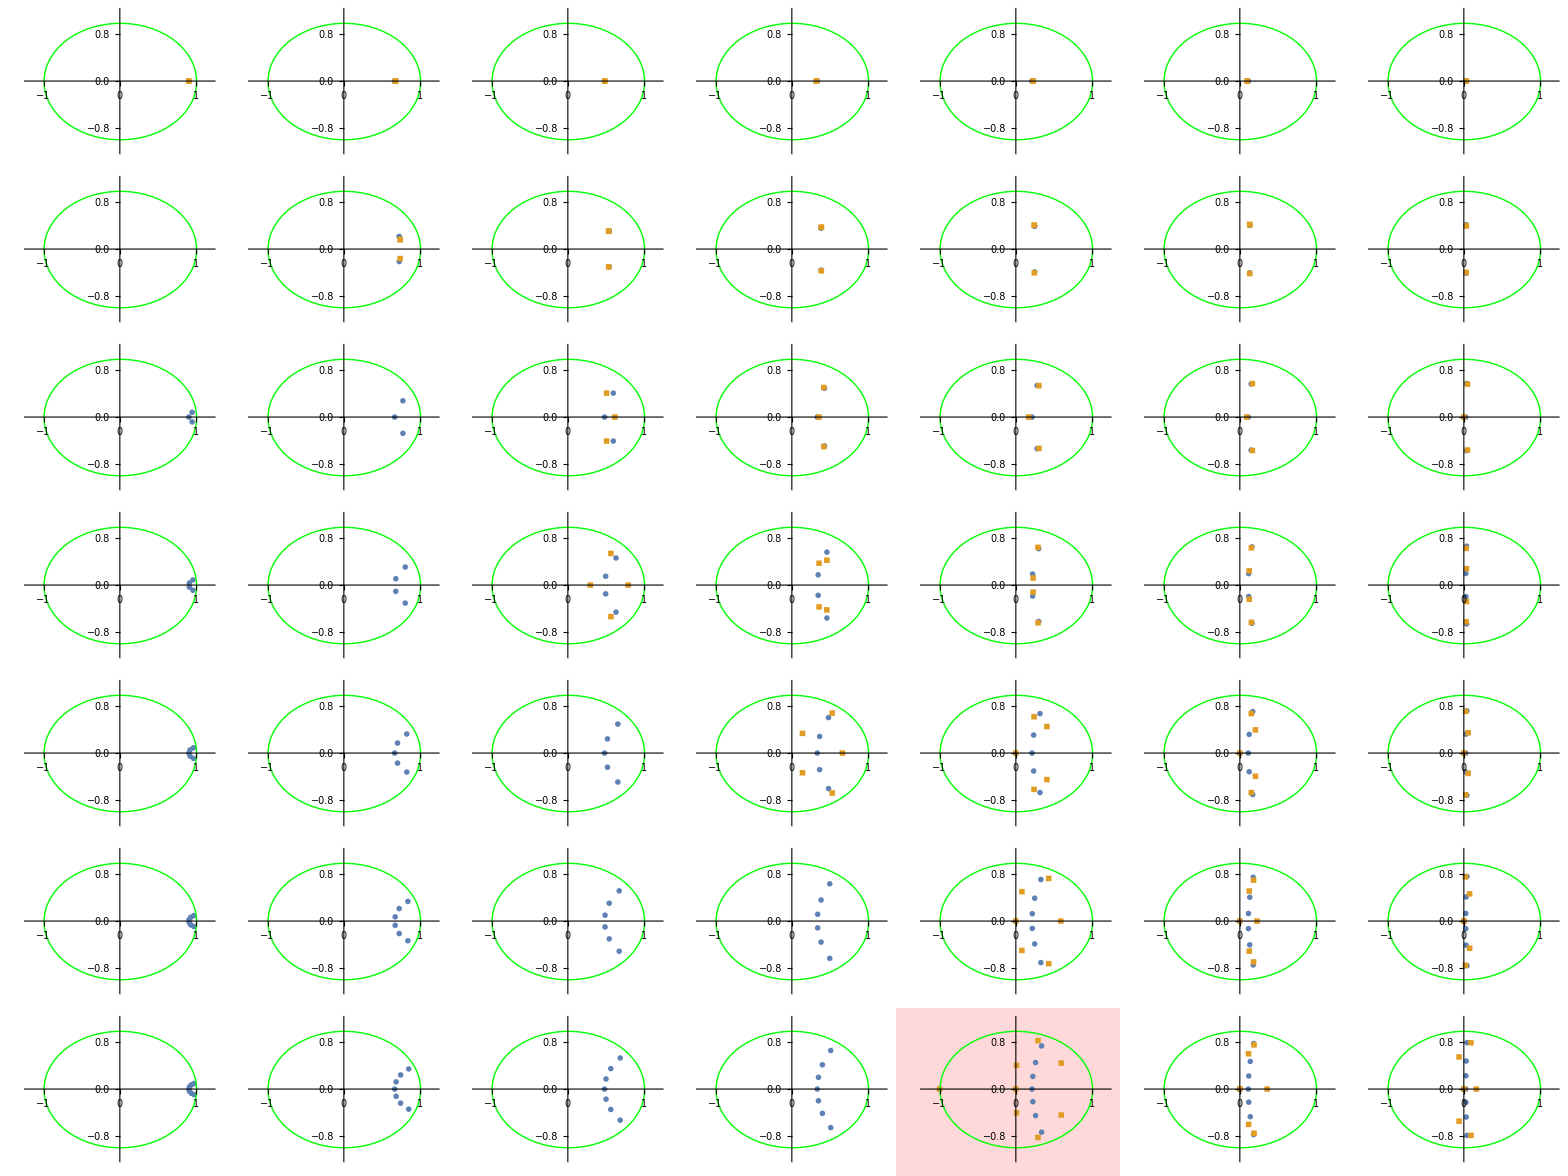

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGbmodels,DGbmodelsDc},2]
```

##### Chebyshev 1

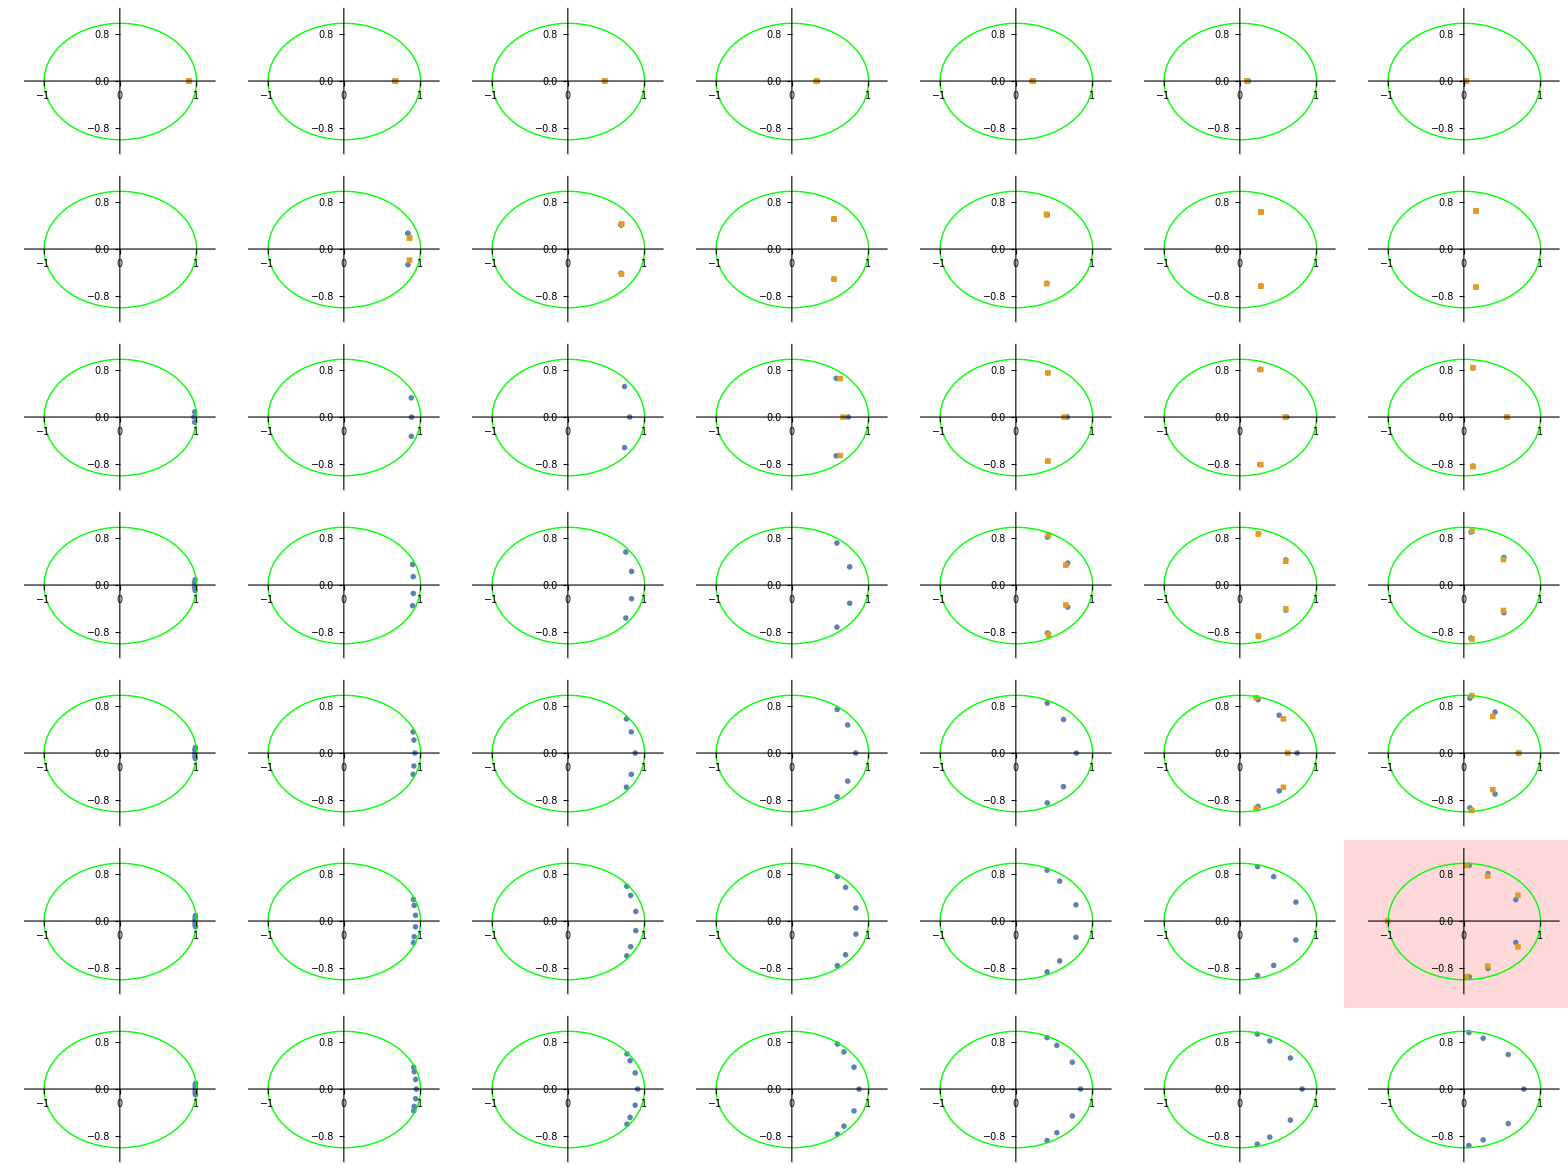

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc1models,DGc1modelsDc},2]
```

##### Chebyshev 2

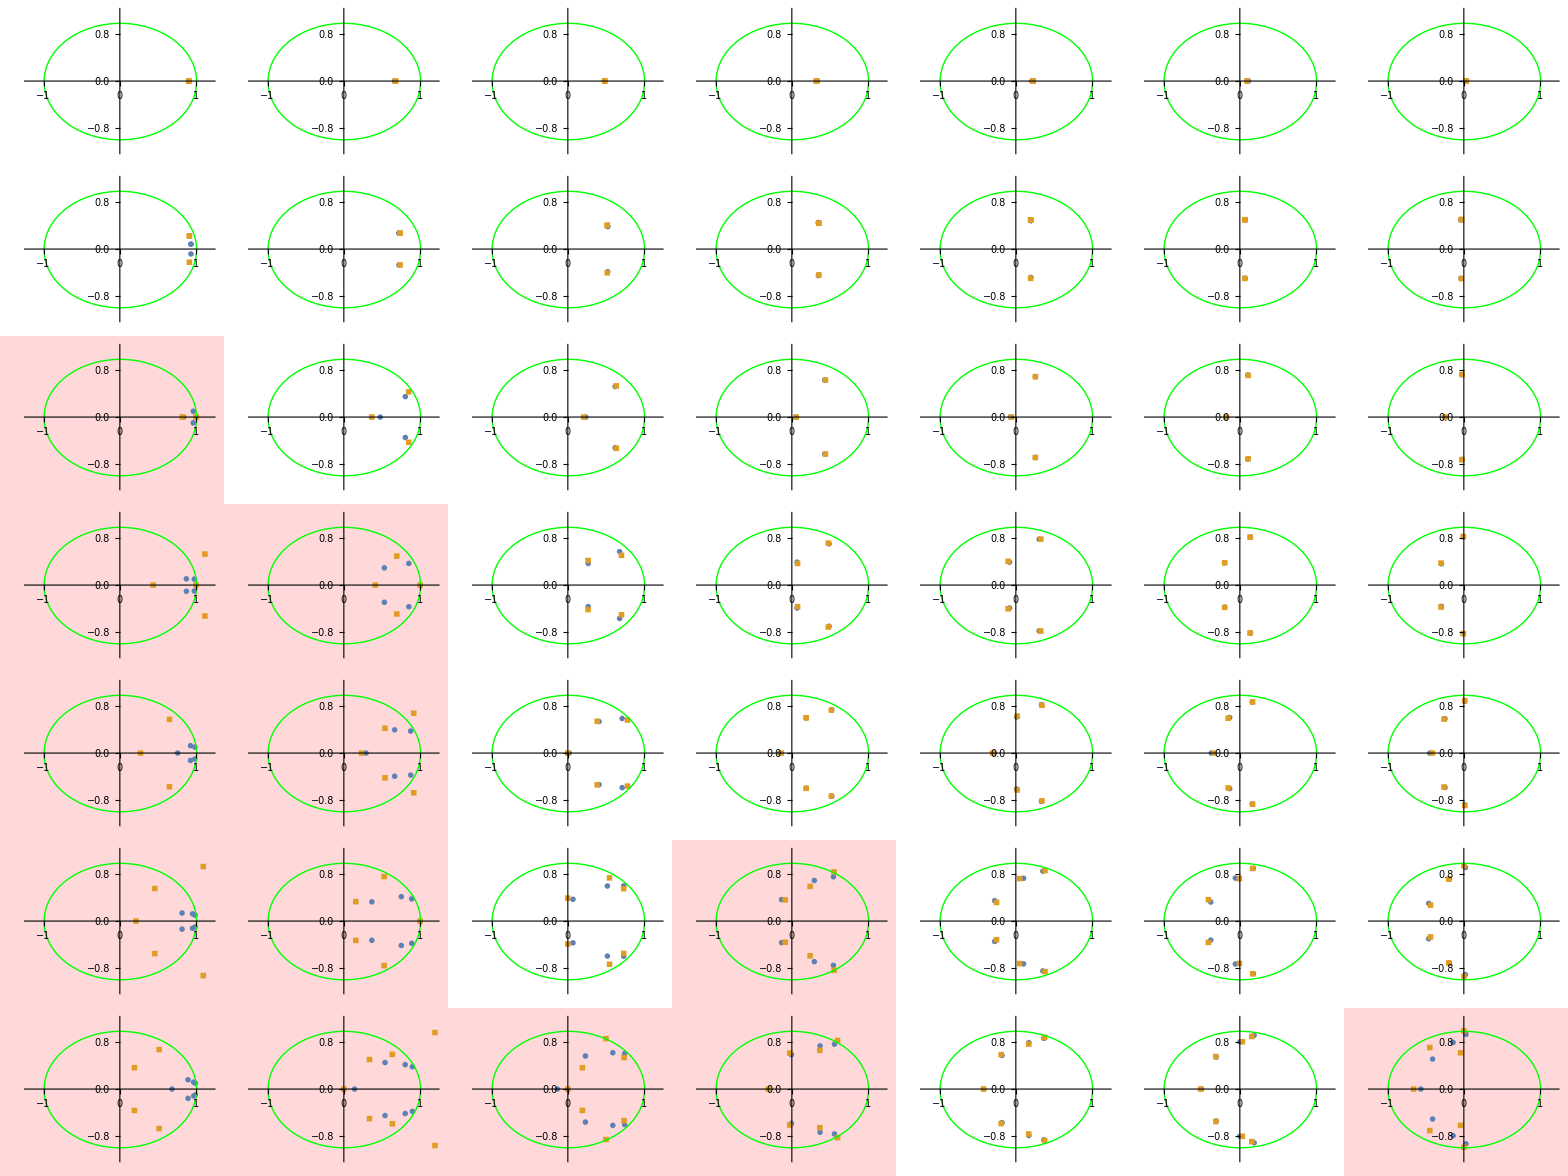

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc2models,DGc2modelsDc},2]
```

##### Eliptic

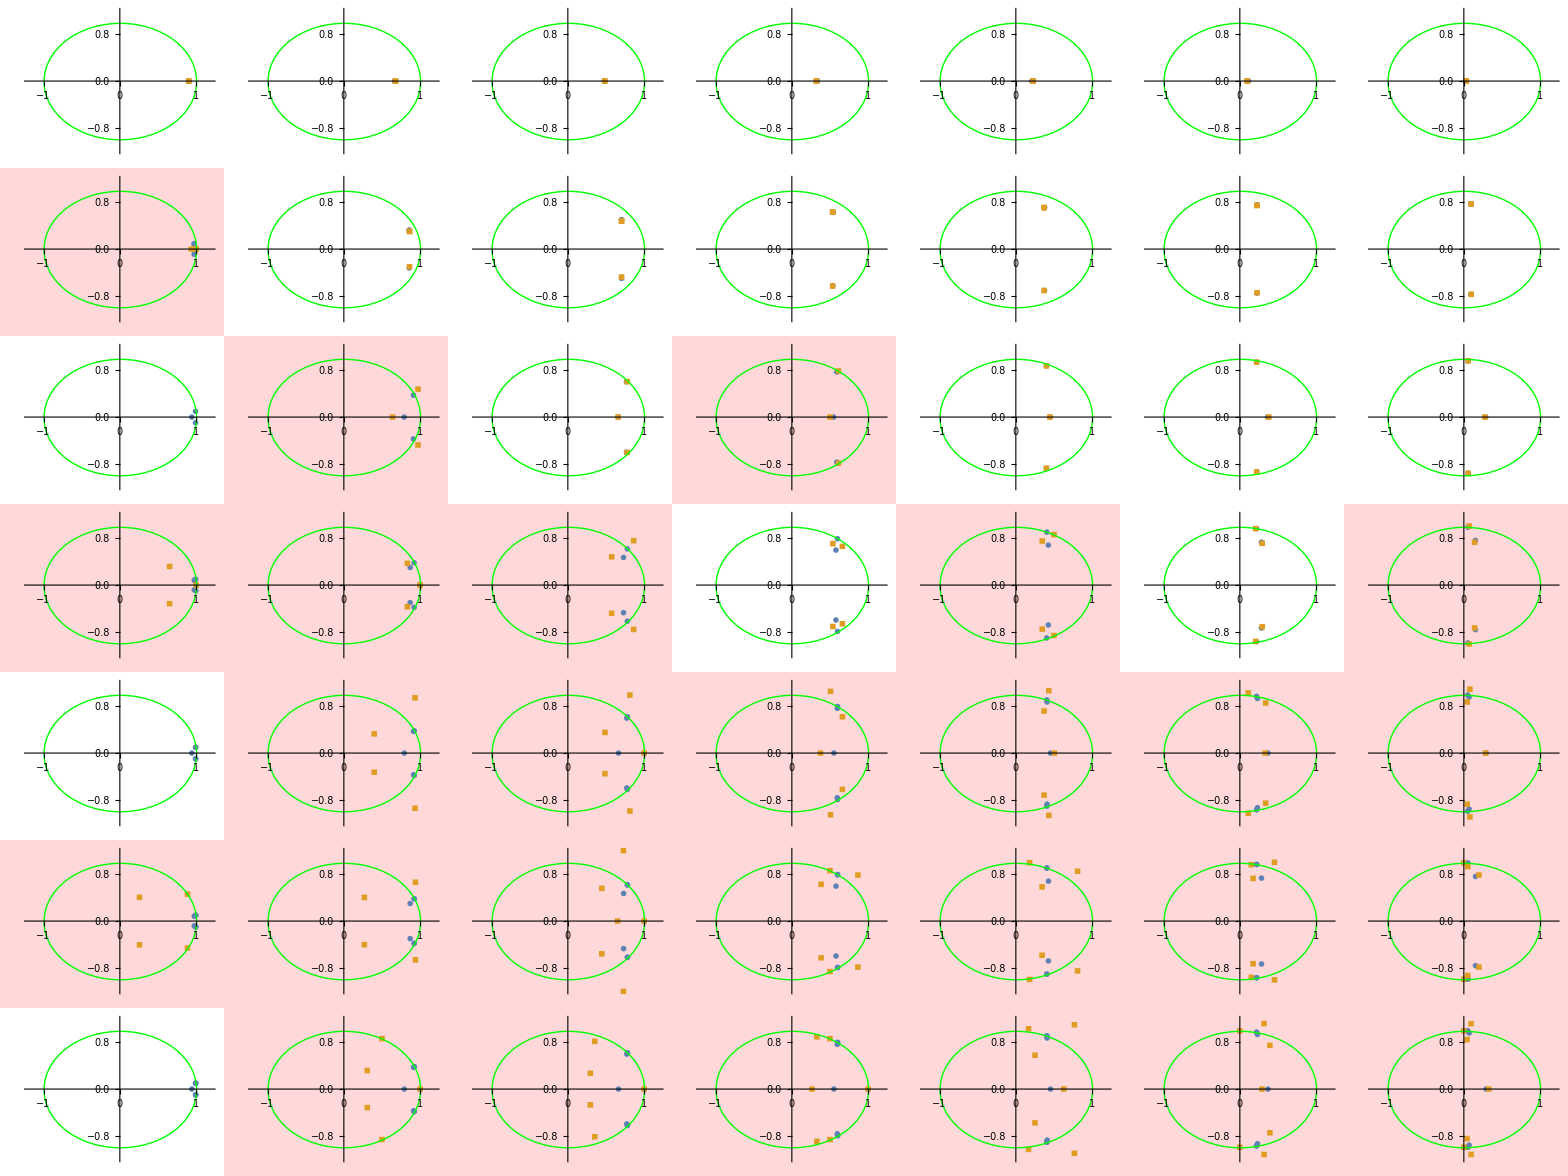

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGemodels,DGemodelsDc},2]
```

### Dyskusja

Istnieje problem polegający na znikaniu licznika (a więc również całego filtru) widoczny jest on przy niskich częstotliwościach filtru Butterwortha i Chebysheva 1
Ponadto widać, iż filtry eliptyczne powyżej 3 rzędu robią się bardzo niestabilne (niektóre nie są zaznaczone na czerwono bo filtr przestał działać z powodów wspomnianych wyżej)

## Główne wyniki dotyczące stabilności

W tej części zostaną przedstawione najważniejsze wyniki dla dyskretyzacji w której wpółczynniki licznika i mianownika są dyskretyzowane razem.

Wizualizacja stabilności filtrów rządzi się zasada jest ta sama - w dół rośnie rząd, w prawo rośnie częstość graniczna.
Promień pierścienia jest związany z liczbą bitów. Środkowy okrąg jest 5 bitowy, każdy kolejny 3 bity więcej, okręgów jest 9, zatem ostatni okrąg reprezentuje 5+9*3=5+27=32 bity. Kolor niebieski oznacza filtr stabilny, kolor pomarańczowy - niestabilny.

```mathematica
SP[p_]:=If[Length[p]>0,If[Count[p,_?(Abs[#]≥1&),{1}]>0,Lighter[Orange],LightBlue],Black];
```

```mathematica
StableOrNot[p1_,p2_,p3_,p4_,p5_,p6_,p7_,p8_,p9_]:=Graphics[{SP[p1],Disk[{0,0}],
EdgeForm[Directive[Dashed,Gray]],SP[p2],Disk[{0,0},{0.9,0.9}],
EdgeForm[Directive[Dashed,Gray]],SP[p3],Disk[{0,0},{0.8,0.8}],
EdgeForm[Directive[Dashed,Gray]],SP[p4],Disk[{0,0},{0.7,0.7}],
EdgeForm[Directive[Dashed,Gray]],SP[p5],Disk[{0,0},{0.6,0.6}],
EdgeForm[Directive[Dashed,Gray]],SP[p6],Disk[{0,0},{0.5,0.5}],
EdgeForm[Directive[Dashed,Gray]],SP[p7],Disk[{0,0},{0.4,0.4}],
EdgeForm[Directive[Dashed,Gray]],SP[p8],Disk[{0,0},{0.3,0.3}],
EdgeForm[Directive[Dashed,Gray]],SP[p9],Disk[{0,0},{0.2,0.2}]}]
```

### Butterworth

```mathematica
Allb=Table[Map[ExtractPoles[DiscretizeModelCoeffs[#,bits]]&,DGbmodels,{2}],{bits,5,32,3}];
```

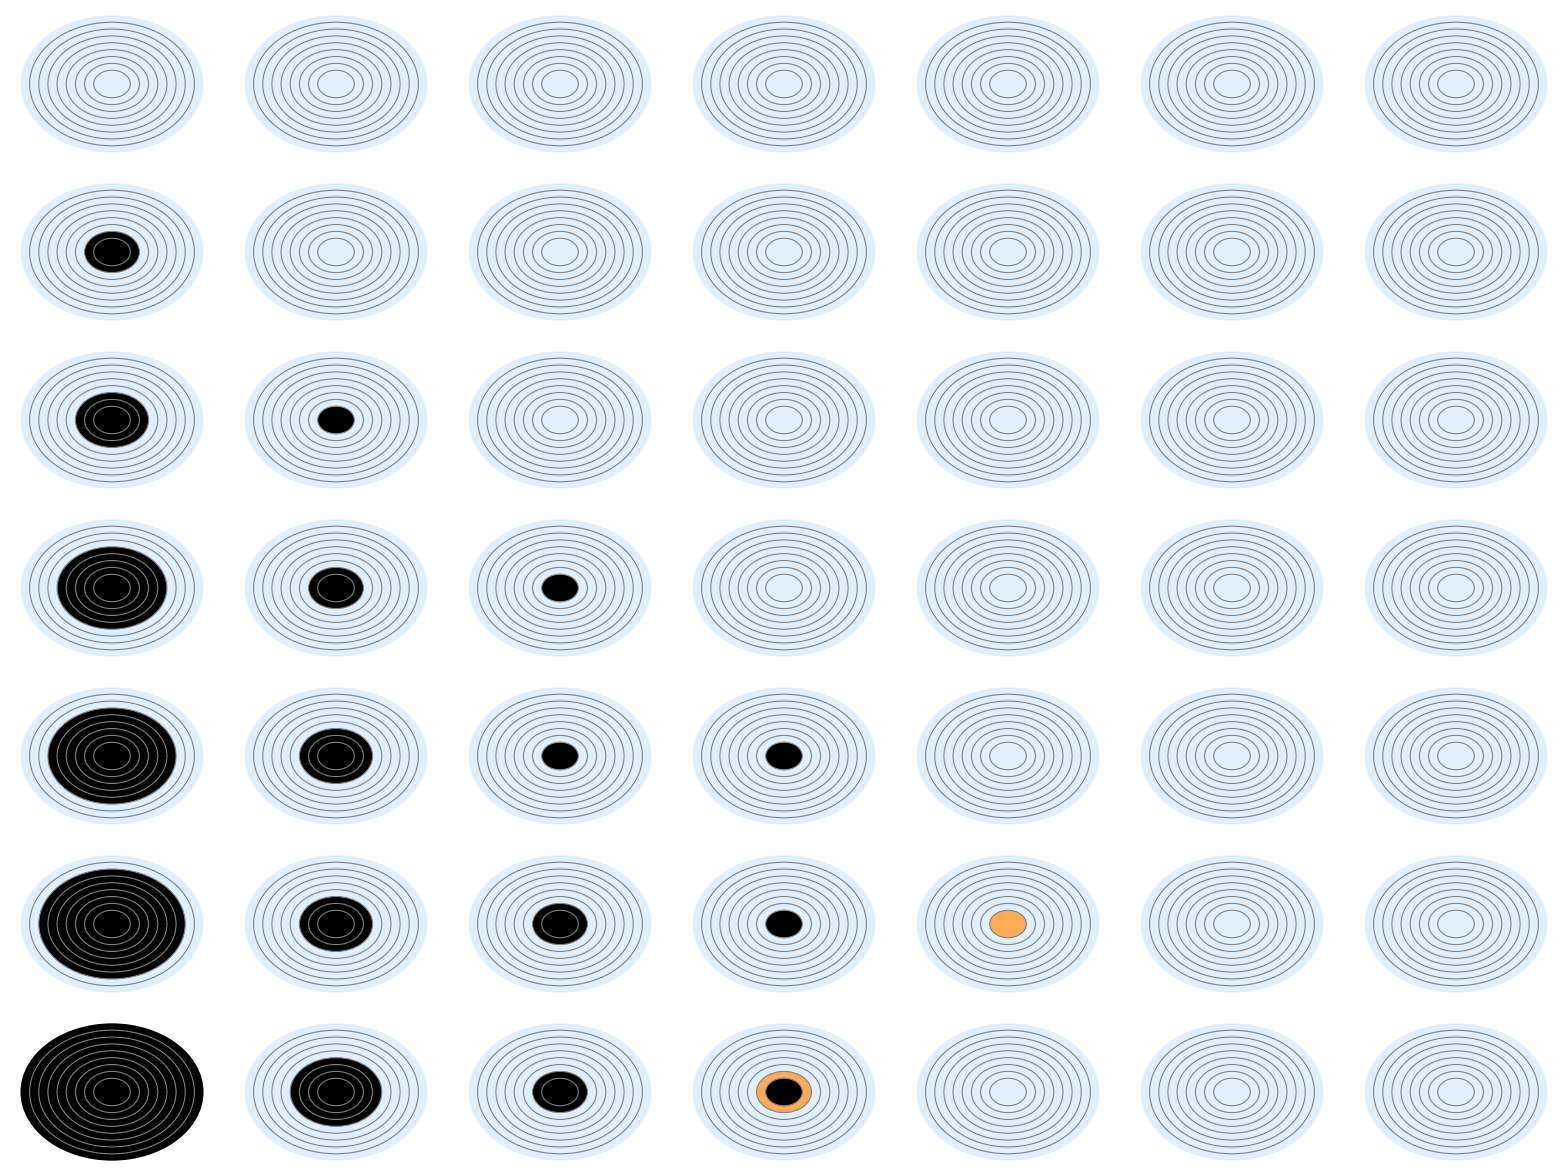

```mathematica
Grid[MapThread[StableOrNot[#9,#8,#7,#6,#5,#4,#3,#2,#1]&,Allb,2],ItemSize->10]
```

### Chebyshev 1

```mathematica
Allc1=Table[Map[ExtractPoles[DiscretizeModelCoeffs[#,bits]]&,DGc1models,{2}],{bits,5,32,3}];
```

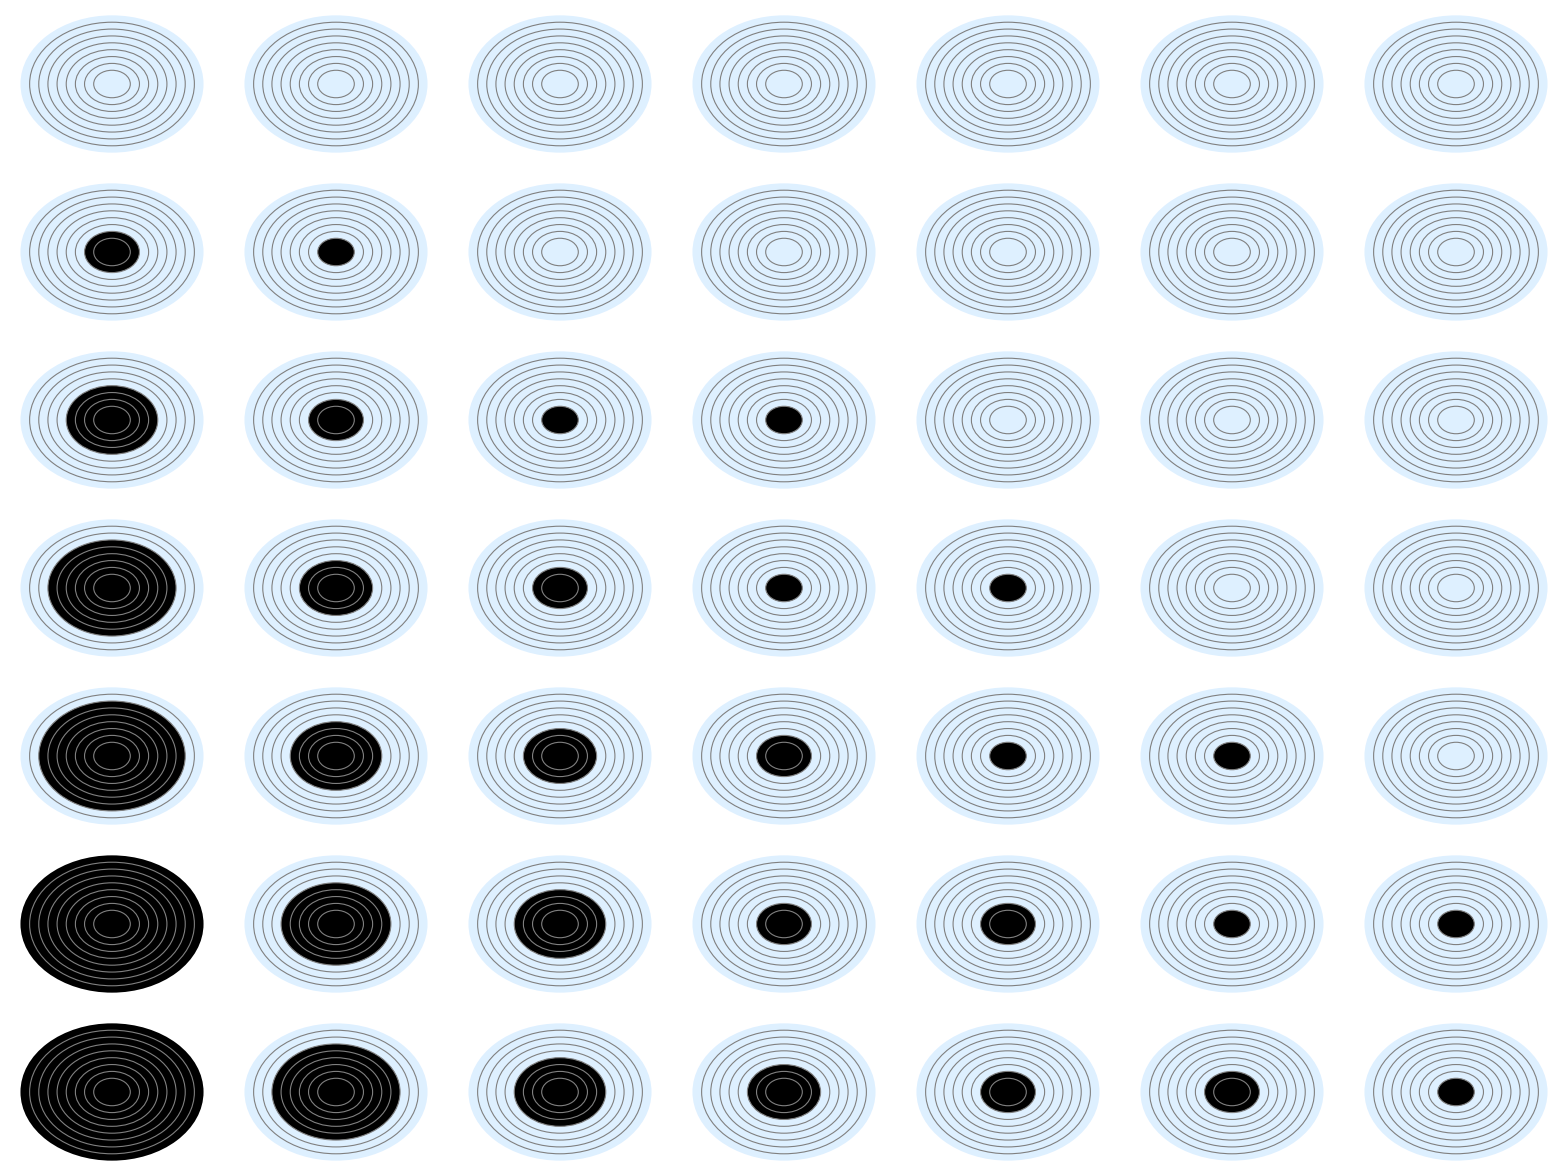

```mathematica
Grid[MapThread[StableOrNot[#9,#8,#7,#6,#5,#4,#3,#2,#1]&,Allc1,2],ItemSize->10]
```

### Chebyshev 2

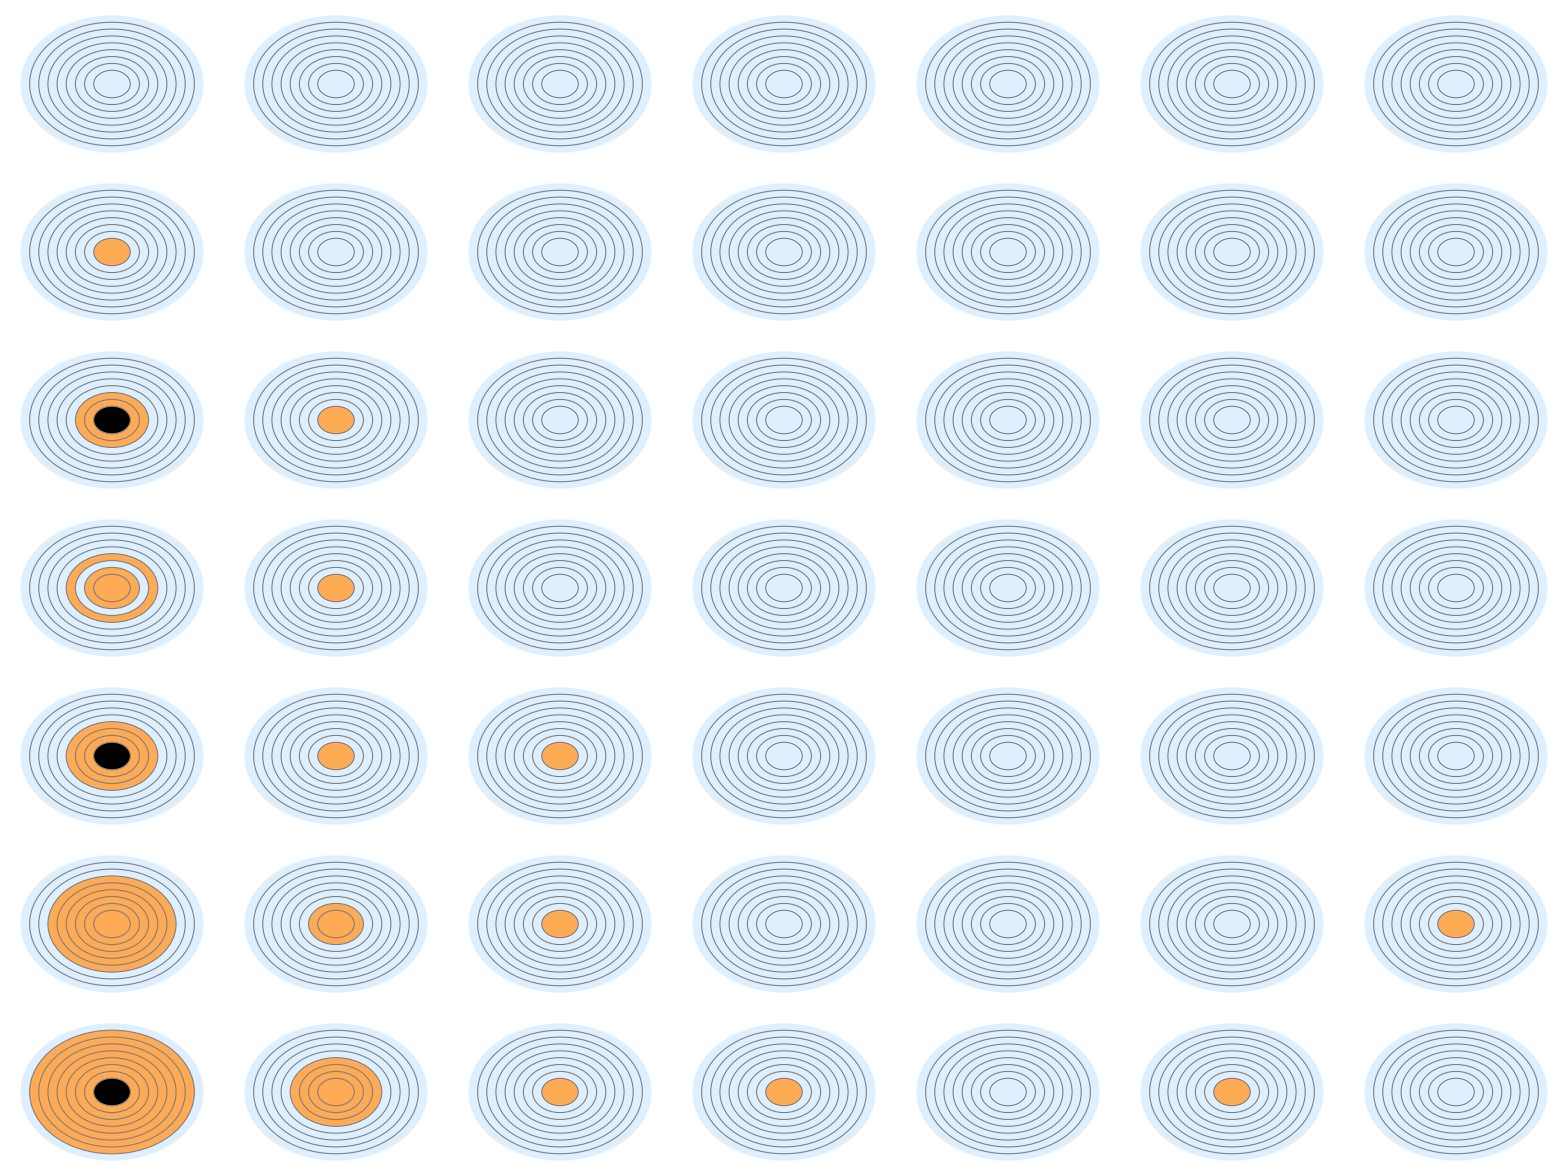

```mathematica
Allc2=Table[Map[ExtractPoles[DiscretizeModelCoeffs[#,bits]]&,DGc2models,{2}],{bits,5,32,3}];
Grid[MapThread[StableOrNot[#9,#8,#7,#6,#5,#4,#3,#2,#1]&,Allc2,2],ItemSize->10]
```

### Eliptyczny

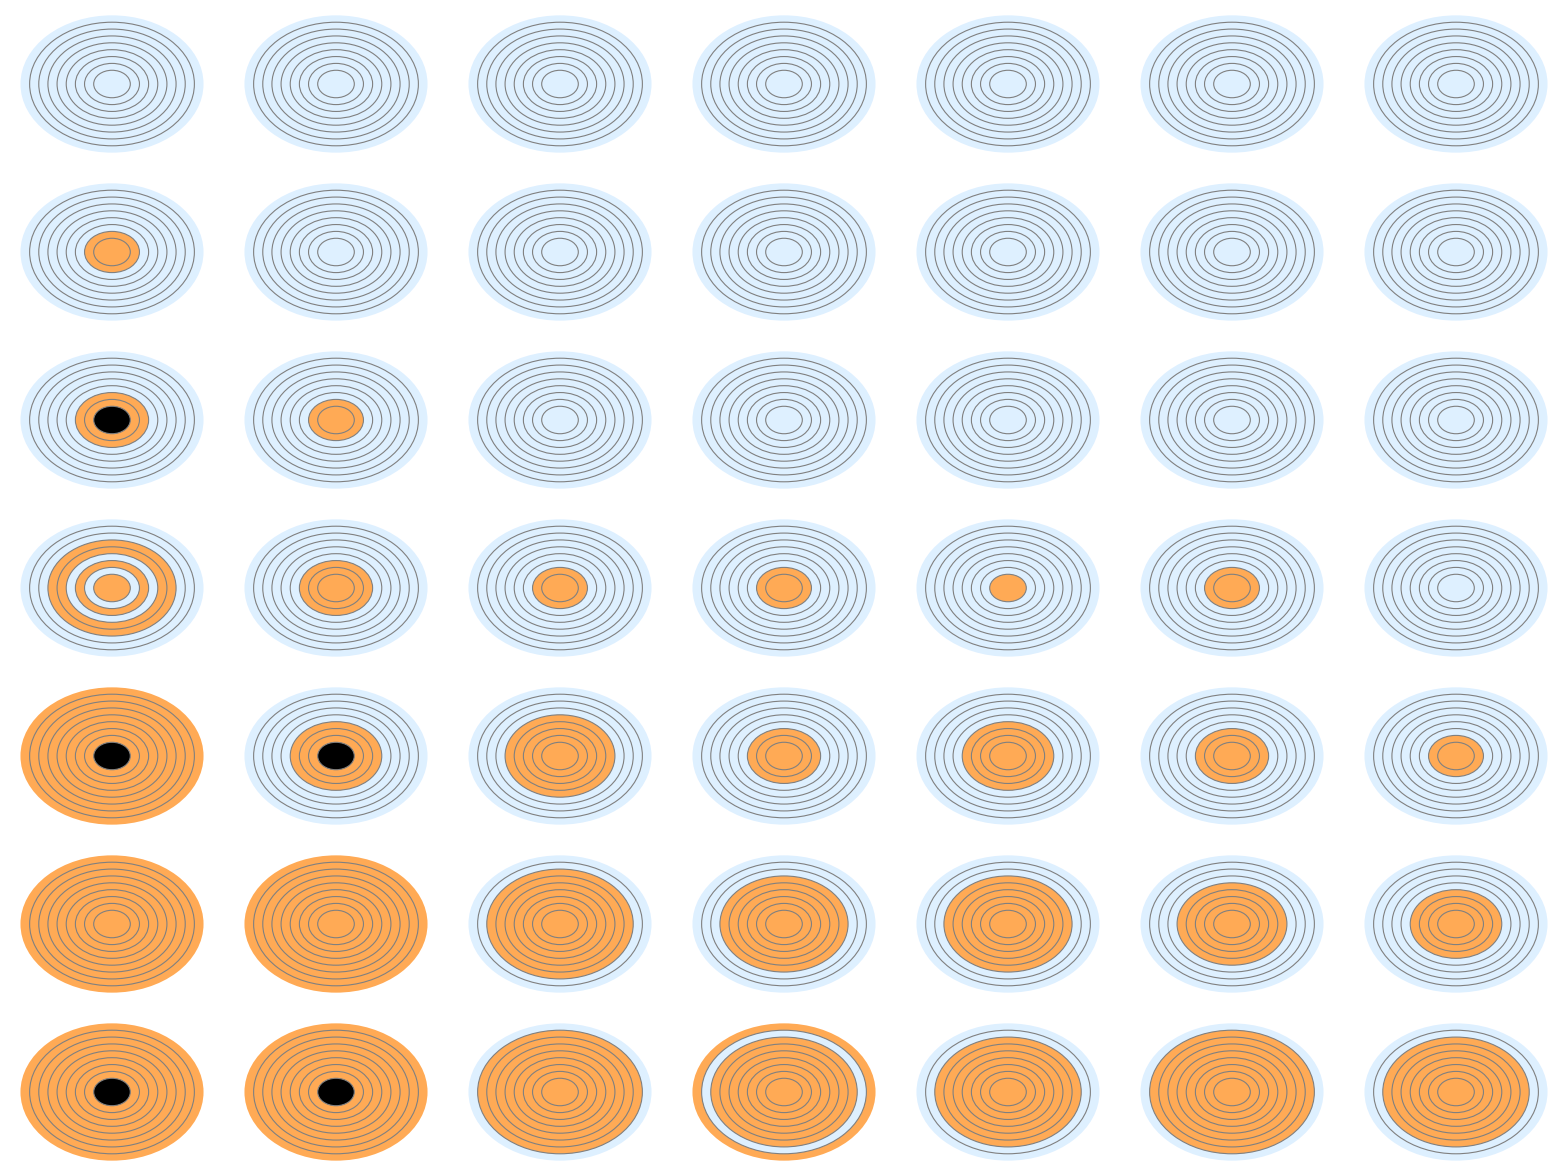

```mathematica
Alle=Table[Map[ExtractPoles[DiscretizeModelCoeffs[#,bits]]&,DGemodels,{2}],{bits,5,32,3}];
Grid[MapThread[StableOrNot[#9,#8,#7,#6,#5,#4,#3,#2,#1]&,Alle,2],ItemSize->10]
```